```mathematica
Pb1[q_,Rg_,nu_,xi_,alpha_]:=Module[{mu=1/nu-1,qb=q*xi/(Erf[q*Rg/Sqrt[6]]^3),c=4 π (xi)^(-1/nu) Cos[π/(2 nu)] Gamma[-1+1/nu]},4*Pi*alpha*mu*Gamma[mu]/(mu*qb)*Sin[mu*ArcTan[qb]]/(1+qb^2)^(mu/2)/c]
```

```mathematica
Pb2[q_,Rg_,nu_,f_,alpha_]:=Module[{mu=1/nu-1,qb=q*2*Rg/Sqrt[f],c=2^(2-1/nu) f^(1/2/nu) π (Rg)^(-1/nu) Cos[π/(2 nu)] Gamma[-1+1/nu]},4*Pi*alpha*Gamma[mu]/qb*Sin[mu*ArcTan[qb]]/(1+qb^2)^(mu/2)/c]
```

```mathematica
FullSimplify[Normal[Series[Pb2[q,Rg,nu,f,alpha],{q,Infinity,1}]],Assumptions->Rg>0]
```

-(2 alpha π (1+(4 q^2 Rg^2)/f)^((-1+nu)/(2 nu)) Cos[π/(2 nu)] Gamma[-1+1/nu])/(√(1/f) q Rg)

```mathematica
FullSimplify[-(2 alpha π ((4 q^2 Rg^2)/f)^((-1+nu)/(2 nu)) Cos[π/(2 nu)] Gamma[-1+1/nu])/(√(1/f) q Rg),Assumptions->f>0&&nu<1&&nu>0&&Rg>0&&q>0]
```

-2^(2-1/nu) alpha f^(1/2/nu) π (q Rg)^(-1/nu) Cos[π/(2 nu)] Gamma[-1+1/nu]

```mathematica
FullSimplify[Normal[Series[Pb1[q,Rg,nu,xi,alpha],{q,Infinity,0}]],Assumptions->Rg>0]
```

$Aborted

```mathematica
FullSimplify[-(4 alpha π (q^2 xi^2)^((-1+nu)/(2 nu)) Gamma[-1+1/nu] Sin[((-1+nu) ArcTan[(ⅇ^((q^2 Rg^2)/2) q^4 Rg^3 xi)/((ⅇ^((q^2 Rg^2)/6) q Rg)^3)])/nu])/(q xi),Assumptions->xi>0&&nu<1&&nu>0&&Rg>0&&q>0]
```

-4 alpha π (q xi)^(-1/nu) Gamma[-1+1/nu] Sin[((-1+nu) ArcTan[q xi])/nu]

```mathematica
FullSimplify[-4 alpha π (q xi)^(-1/nu) Gamma[-1+1/nu] Sin[((-1+nu) Pi/2)/nu]]
```

-4 alpha π (q xi)^(-1/nu) Cos[π/(2 nu)] Gamma[-1+1/nu]

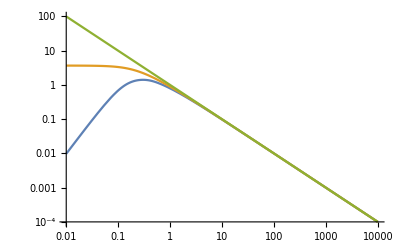

```mathematica
LogLogPlot[{Pb1[q,10,2.9999/3,3,1],Pb2[q,10,2.9999/3,12,1],q^(-1/(3/3))},{q,0.01,10^4},PlotRange->All]
```

```mathematica
Simplify[Limit[Pb2[q,Rg,nu,f,alpha],nu->1],Assumptions->q>0&&f>0&&Rg>0&&alpha>0]
```

(2 alpha ArcTan[(2 q Rg)/(√f)])/(π q)

```mathematica
FullSimplify[Normal[Series[Pb2[q,Rg,nu,f,alpha],{q,0,0}]],Assumptions->Reals[nu] && nu>1/3&&nu<=1&f>0&&Rg>0&&alpha>0]
```

2^(1/nu) alpha f^(-1/2/nu) (-1+1/nu) Rg^(1/nu) Sec[π/(2 nu)]

```mathematica
FullSimplify[Limit[Pb1[q,Rg,nu,xi,alpha],nu->1],Assumptions->q>0&&xi>0&&Rg>0&&alpha>0]
```

(2 alpha ArcTan[(q xi)/Erf[(q Rg)/(√6)]^3] Erf[(q Rg)/(√6)]^3)/(π q)

```mathematica
FullSimplify[Limit[Pb1[q,Rg,nu,xi,alpha],q->0,Assumptions->nu>0&&xi>0&&Rg>0&&alpha>0],Assumptions->nu>0&&xi>0&&Rg>0&&alpha>0]
```

0